```mathematica
SetDirectory["~/Dropbox/Posttraumatic Medoids Disorder/CodeForPaper/"]
```

/Users/anellore/Dropbox/Posttraumatic Medoids Disorder/CodeForPaper

```mathematica
r2k2 = Import["r2_k_2.csv"];unik2=Import["uniform_k_2.csv"];r2k3 = Import["r2_k_3.csv"];unik3 = Import["uniform_k_3.csv"];
```

```mathematica
f[x_]:=Transpose[{Transpose[x][[1]], Transpose[x][[2]], Transpose[x][[3]],1000-Transpose[x][[4]], 1000-Transpose[x][[5]]}]
```

```mathematica
(*r2k2data=Release[Table[Hold[Select[Select[f[r2k2], #[[1]]==2 &][[All, {2,3,4,5}]], #[[2]]==j&][[All,{3,4}]]]/.j->i, {i, 2, 5, .2}]];r2k2data=Flatten[Table[{r2k2data[[i]],{{0}}}, {i, 1, Length[r2k2data]}],2]*)
```

```mathematica
s = {2,3,4,10};r2k2databall=Table[0,{k,1,4}];r2k3databall=Table[0,{k,1,4}];unik2databall=Table[0,{k,1,4}];unik3databall=Table[0,{k,1,4}];For[k=1, k≤4, k++, r2k2databall[[k]]=Release[Table[Hold[Select[Select[f[r2k2], #[[1]]==s[[k]] &][[All, {2,3,4,5}]], #[[1]]==j&][[All,{2,4}]]]/.j->i, {i, 5, 30, 5}]];];For[k=1, k≤4, k++, unik2databall[[k]]=Release[Table[Hold[Select[Select[f[unik2], #[[1]]==s[[k]] &][[All, {2,3,4,5}]], #[[1]]==j&][[All,{2,4}]]]/.j->i, {i, 5, 30, 5}]];];
For[k=1, k≤4, k++, r2k3databall[[k]]=Release[Table[Hold[Select[Select[f[r2k3], #[[1]]==s[[k]] &][[All, {2,3,4,5}]], #[[1]]==j&][[All,{2,4}]]]/.j->i, {i, 5, 30, 5}]];];
For[k=1, k≤4, k++, unik3databall[[k]]=Release[Table[Hold[Select[Select[f[unik3], #[[1]]==s[[k]] &][[All, {2,3,4,5}]], #[[1]]==j&][[All,{2,4}]]]/.j->i, {i, 5, 30, 5}]];];
```

```mathematica
RGBColor[227/256,29/256,118/256]
```

RGBColor[227/256,29/256,59/128]

```mathematica
RGBColor[0/256,179/256,220/256]
```

RGBColor[0,179/256,55/64]

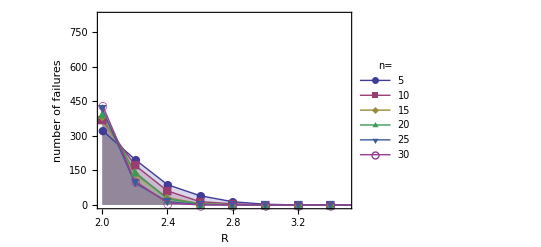
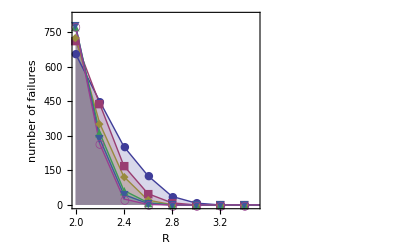
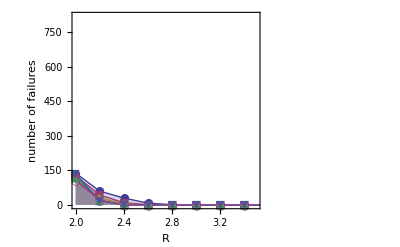
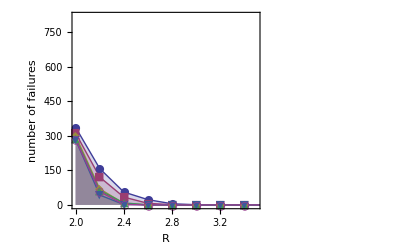
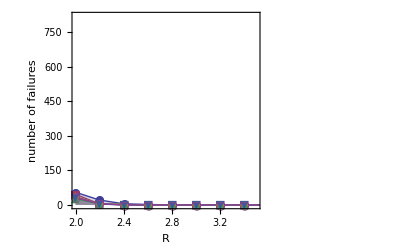
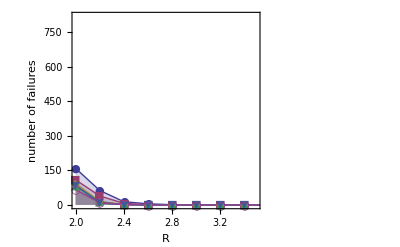
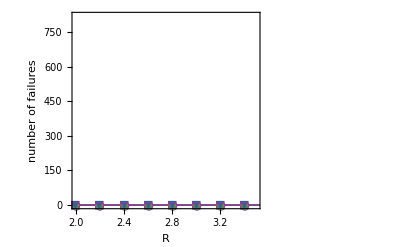
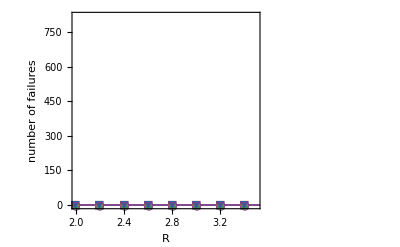

```mathematica
nolabels={{ListLinePlot[{r2k2databall[[1]][[1]],r2k2databall[[1]][[2]],r2k2databall[[1]][[3]],r2k2databall[[1]][[4]],r2k2databall[[1]][[5]],r2k2databall[[1]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,PlotLegends->Placed[LineLegend[{Style["5",FontFamily->"Futura"],Style["10",FontFamily->"Futura"],Style["15",FontFamily->"Futura"],Style["20",FontFamily->"Futura"],Style["25",FontFamily->"Futura"],Style["30",FontFamily->"Futura"]},LegendLabel->Style["n=",FontFamily->"Futura"], LegendLayout->{"Row",2}],{.5,.5}],FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]},FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}],ListLinePlot[{r2k3databall[[1]][[1]],r2k3databall[[1]][[2]],r2k3databall[[1]][[3]],r2k3databall[[1]][[4]],r2k3databall[[1]][[5]],r2k3databall[[1]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}]},{ListLinePlot[{r2k2databall[[2]][[1]],r2k2databall[[2]][[2]],r2k2databall[[2]][[3]],r2k2databall[[2]][[4]],r2k2databall[[2]][[5]],r2k2databall[[2]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}],ListLinePlot[{r2k3databall[[2]][[1]],r2k3databall[[2]][[2]],r2k3databall[[2]][[3]],r2k3databall[[2]][[4]],r2k3databall[[2]][[5]],r2k3databall[[2]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}]},{ListLinePlot[{r2k2databall[[3]][[1]],r2k2databall[[3]][[2]],r2k2databall[[3]][[3]],r2k2databall[[3]][[4]],r2k2databall[[3]][[5]],r2k2databall[[3]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}],ListLinePlot[{r2k3databall[[3]][[1]],r2k3databall[[3]][[2]],r2k3databall[[3]][[3]],r2k3databall[[3]][[4]],r2k3databall[[3]][[5]],r2k3databall[[3]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}]},{ListLinePlot[{r2k2databall[[4]][[1]],r2k2databall[[4]][[2]],r2k2databall[[4]][[3]],r2k2databall[[4]][[4]],r2k2databall[[4]][[5]],r2k2databall[[4]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}],ListLinePlot[{r2k3databall[[4]][[1]],r2k3databall[[4]][[2]],r2k3databall[[4]][[3]],r2k3databall[[4]][[4]],r2k3databall[[4]][[5]],r2k3databall[[4]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}]}}
```

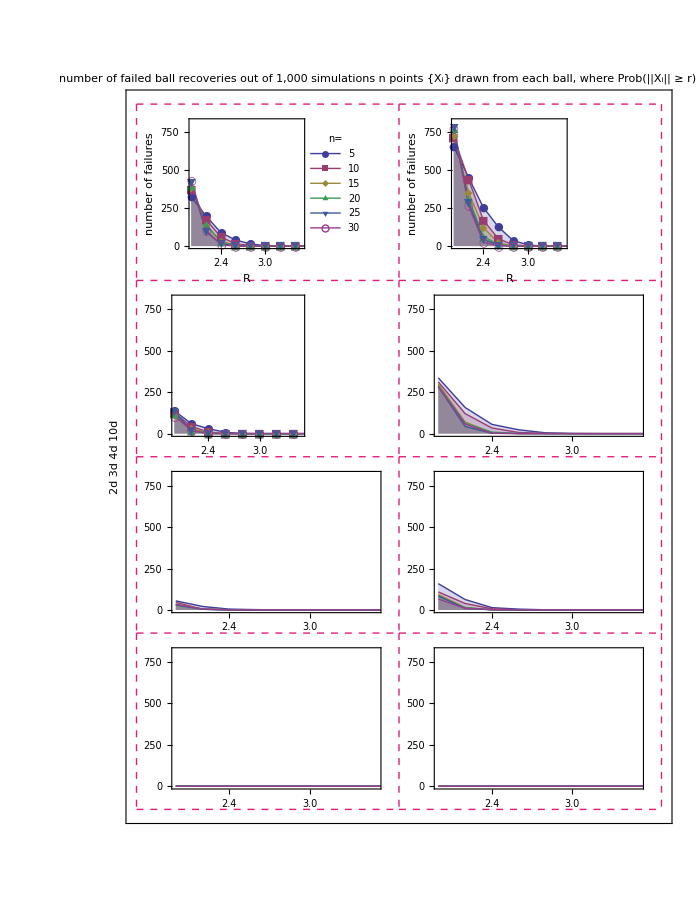

```mathematica
r2grid=Show[GraphicsGrid[nolabels, PlotLabel->Style[Grid[{{"number of failed ball recoveries out of 1,000 simulations"},{"n points {X_i} drawn from each ball, where Prob(||X_i|| ≥ r) = 1 - r^2"}}],15, FontFamily->"Futura"], ImageSize->{700,900}, Frame->All, FrameStyle->Directive[Dashed,RGBColor[227/256,29/256,118/256]]], Frame->True,FrameStyle->White,FrameTicks->False,FrameLabel->{{Text[Style[Grid[{{},{},{"2d"},{},{},{},{},{},{},{},{"3d"},{},{},{},{},{},{},{},{"4d"},{},{},{},{},{},{},{},{"10d"},{},{}}], FontFamily->"Futura", FontSize->17, RGBColor[227/256,29/256,118/256]]],""},{"",Style["        two balls                                            three balls    ", FontFamily->"Futura", FontSize->17, RGBColor[227/256,29/256,118/256]]}}, RotateLabel->False]
```

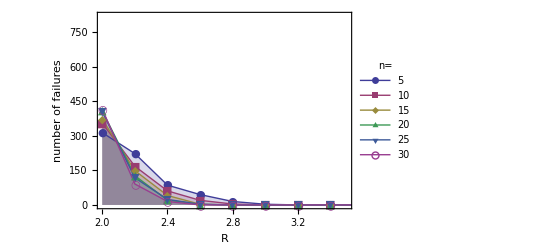
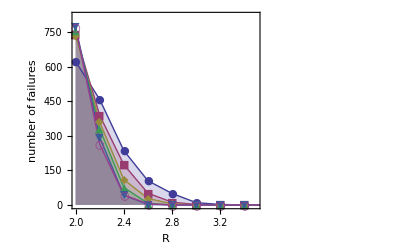
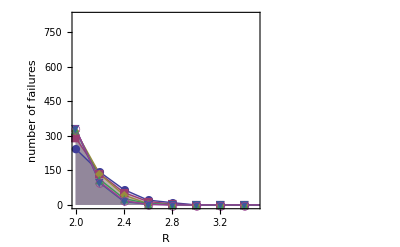
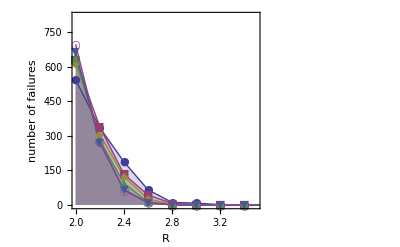
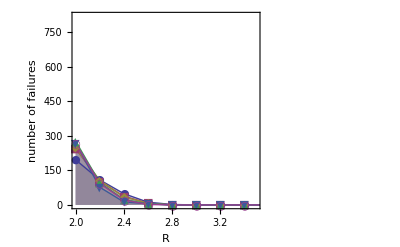
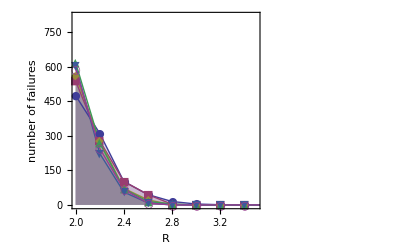
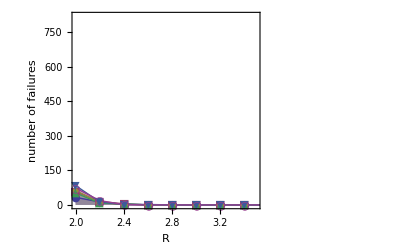
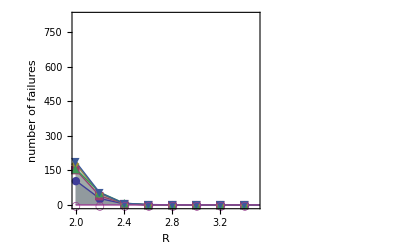

```mathematica
nolabelsuni={{ListLinePlot[{unik2databall[[1]][[1]],unik2databall[[1]][[2]],unik2databall[[1]][[3]],unik2databall[[1]][[4]],unik2databall[[1]][[5]],unik2databall[[1]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,PlotLegends->Placed[LineLegend[{Style["5",FontFamily->"Futura"],Style["10",FontFamily->"Futura"],Style["15",FontFamily->"Futura"],Style["20",FontFamily->"Futura"],Style["25",FontFamily->"Futura"],Style["30",FontFamily->"Futura"]},LegendLabel->Style["n=",FontFamily->"Futura"], LegendLayout->{"Row",2}],{.5,.5}],FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]},FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}],ListLinePlot[{unik3databall[[1]][[1]],unik3databall[[1]][[2]],unik3databall[[1]][[3]],unik3databall[[1]][[4]],unik3databall[[1]][[5]],unik3databall[[1]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}]},{ListLinePlot[{unik2databall[[2]][[1]],unik2databall[[2]][[2]],unik2databall[[2]][[3]],unik2databall[[2]][[4]],unik2databall[[2]][[5]],unik2databall[[2]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}],ListLinePlot[{unik3databall[[2]][[1]],unik3databall[[2]][[2]],unik3databall[[2]][[3]],unik3databall[[2]][[4]],unik3databall[[2]][[5]],unik3databall[[2]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}]},{ListLinePlot[{unik2databall[[3]][[1]],unik2databall[[3]][[2]],unik2databall[[3]][[3]],unik2databall[[3]][[4]],unik2databall[[3]][[5]],unik2databall[[3]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}],ListLinePlot[{unik3databall[[3]][[1]],unik3databall[[3]][[2]],unik3databall[[3]][[3]],unik3databall[[3]][[4]],unik3databall[[3]][[5]],unik3databall[[3]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}]},{ListLinePlot[{unik2databall[[4]][[1]],unik2databall[[4]][[2]],unik2databall[[4]][[3]],unik2databall[[4]][[4]],unik2databall[[4]][[5]],unik2databall[[4]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}],ListLinePlot[{unik3databall[[4]][[1]],unik3databall[[4]][[2]],unik3databall[[4]][[3]],unik3databall[[4]][[4]],unik3databall[[4]][[5]],r2k3databall[[4]][[6]]}, PlotMarkers->{Automatic,Medium}, Filling->Axis, PlotRange->{{2, 3.5}, {0, 820}}, PlotRangeClipping->False, Axes->None, Frame->True,FrameLabel->{"R","number of failures"},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12]}]}}
```

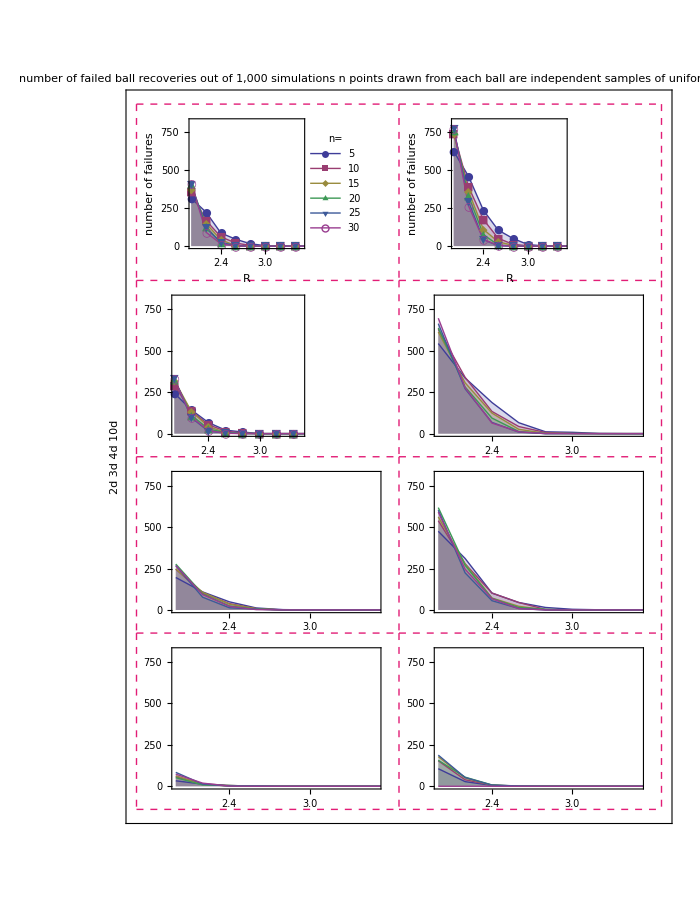

```mathematica
unigrid=Show[GraphicsGrid[nolabelsuni, PlotLabel->Style[Grid[{{"number of failed ball recoveries out of 1,000 simulations"},{"n points drawn from each ball are independent samples of uniform distribution"}}],15, FontFamily->"Futura"], ImageSize->{700,900}, Frame->All, FrameStyle->Directive[Dashed,RGBColor[227/256,29/256,118/256]]], Frame->True,FrameStyle->White,FrameTicks->False,FrameLabel->{{Text[Style[Grid[{{},{},{"2d"},{},{},{},{},{},{},{},{"3d"},{},{},{},{},{},{},{},{"4d"},{},{},{},{},{},{},{},{"10d"},{},{}}], FontFamily->"Futura", FontSize->17, RGBColor[227/256,29/256,118/256]]],""},{"",Style["        two balls                                            three balls    ", FontFamily->"Futura", FontSize->17, RGBColor[227/256,29/256,118/256]]}}, RotateLabel->False]
```

```mathematica
Export["r2grid.pdf",r2grid]
```

r2grid.pdf

```mathematica
Export["unigrid.pdf", unigrid]
```

unigrid.pdf